# Solución Problema 1E

## A partir del enunciado del problema 1D, considerando las pérdidas localizadas (ver los valores de K en la figura) y las pérdidas por fricción,determine la curva características del sistema (grafique Ht vs Q). Para este caso asuma que el tanque está abierto a la atmosféra y que en el primer tramo de tubería se ha instalado una bomba centrífuga.

# Datos de entrada

```mathematica
P2=40*10^3;z1=26;z2=160;ρ=1000;g=9.81;γ=ρ*g;D0=150/1000;f=0.015;Clear[Q]
```

# Solución Punto a)

```mathematica
V=Q/(π/4*D0^2)//N
```

56.5884 Q

```mathematica
E1=z1
```

26

```mathematica
E2=P2/γ+z2+V^2/(2g)
```

164.077+163.214 Q^2

```mathematica
hk=V^2/(2g)*(0.4+0.9+1)
```

375.391 Q^2

```mathematica
hf=(f*(325+160+260))/D0 V^2/(2g)
```

12159.4 Q^2

## Creación en blanco de una matrix .

```mathematica
Tabla1=Table[0,{i,1,20},{i,1,2}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

## Definición de diferentes magnitudes de caudales.

```mathematica
For[i=1, i<21,i++,Tabla1[[i,1]]=0.005*i;Tabla1[[i,2]]=Ht/.Solve[26+Ht-2.3*((Tabla1[[i,1]]/(π/4*D0^2))^2)/(2*9.81)-(0.015*(325+160+260))/D0*((Tabla1[[i,1]]/(π/4*D0^2))^2)/(2*9.81)==((Tabla1[[i,1]]/(π/4*D0^2))^2)/(2*9.81)+(40*10^3)/(1000*9.81)+160,Ht][[1]]];
MatrixForm[Tabla1]
```

(0.005 | 138.395
0.01 | 139.347
0.015 | 140.935
0.02 | 143.157
0.025 | 146.014
0.03 | 149.506
0.035 | 153.633
0.04 | 158.394
0.045 | 163.791
0.05 | 169.823
0.055 | 176.489
0.06 | 183.79
0.065 | 191.727
0.07 | 200.298
0.075 | 209.504
0.08 | 219.345
0.085 | 229.821
0.09 | 240.931
0.095 | 252.677
0.1 | 265.058)

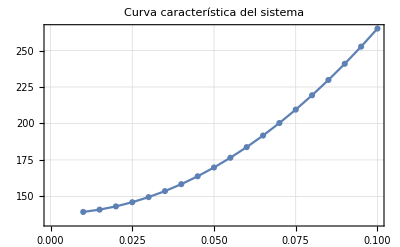

```mathematica
ListLinePlot[Transpose[{Tabla1[[All,1]],Tabla1[[All,2]]}],PlotTheme->"Detailed",PlotLabel->"Curva característica del sistema",PlotMarkers->Automatic]
```

```mathematica
Tabla2=Table[0,{i,1,20},{i,1,2}];Tabla1[[1,1]]="Caudal (m.b3/s)";Tabla1[[1,2]]="Ht (m.c.a)";
```

```mathematica
MatrixForm[Tabla1]
```

(Caudal (m.b3/s) | Ht (m.c.a)
0.01 | 139.347
0.015 | 140.935
0.02 | 143.157
0.025 | 146.014
0.03 | 149.506
0.035 | 153.633
0.04 | 158.394
0.045 | 163.791
0.05 | 169.823
0.055 | 176.489
0.06 | 183.79
0.065 | 191.727
0.07 | 200.298
0.075 | 209.504
0.08 | 219.345
0.085 | 229.821
0.09 | 240.931
0.095 | 252.677
0.1 | 265.058)